```mathematica
Solve[ζ^2+α ζ-1==0,ζ]
```

{{ζ→1/2 (-α-√(4+α^2))},{ζ→1/2 (-α+√(4+α^2))}}

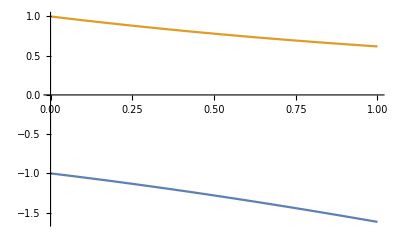

```mathematica
Plot[ζ/.%//Evaluate,{α,0,1}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
L=1;Δx=0.1;χ=1;M=10;
```

```mathematica
T0[x_]= Sin[Pi x/L]
```

Sin[π x]

```mathematica
T[0,n_]=0;
T[M,n_]=0;
```

```mathematica
x[j_]= j Δx
```

0.1 j

```mathematica
Δt=0.1;
```

```mathematica
Clear[sol]
```

```mathematica
sol[0]=Table[T[j,0]-> T0[x[j]],{j,1,M-1}]
```

{T[1,0]→0.309017,T[2,0]→0.587785,T[3,0]→0.809017,T[4,0]→0.951057,T[5,0]→1.,T[6,0]→0.951057,T[7,0]→0.809017,T[8,0]→0.587785,T[9,0]→0.309017}

```mathematica
sol[n_]:= sol[n]=Module[{vars,eqns},
vars=Table[T[j,n],{j,1,M-1}];
eqns=Table[T[j,n]-T[j,n-1]==χ Δt/(2 Δx^2)(T[j+1,n]-2T[j,n]+T[j-1,n]+T[j+1,n-1]-2T[j,n-1]+T[j-1,n-1]),{j,1,M-1}]/.sol[n-1];
Solve[eqns,vars][[1]]]
```

```mathematica
sol[1]
```

{T[1,1]→0.105928,T[2,1]→0.201488,T[3,1]→0.277324,T[4,1]→0.326014,T[5,1]→0.342791,T[6,1]→0.326014,T[7,1]→0.277324,T[8,1]→0.201488,T[9,1]→0.105928}

```mathematica
sol[2]
```

{T[1,2]→0.0363113,T[2,2]→0.0690682,T[3,2]→0.0950642,T[4,2]→0.111755,T[5,2]→0.117506,T[6,2]→0.111755,T[7,2]→0.0950642,T[8,2]→0.0690682,T[9,2]→0.0363113}

```mathematica
Tlist[n_]:=Table[{x[j],T[j,n]},{j,0,M}]/.sol[n]
```

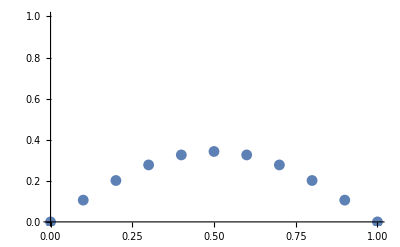
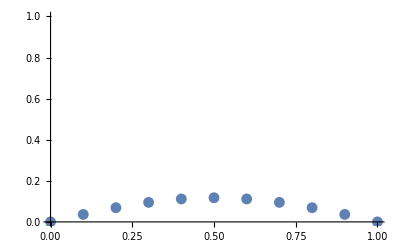
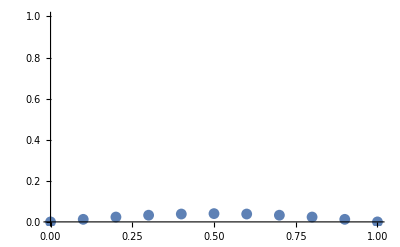
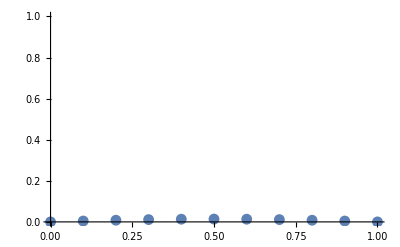
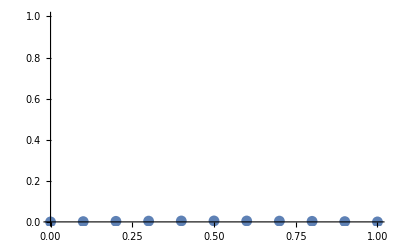
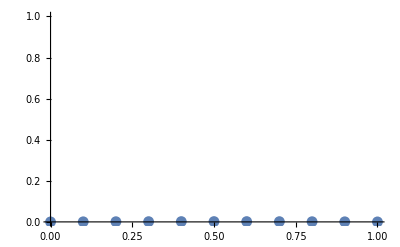
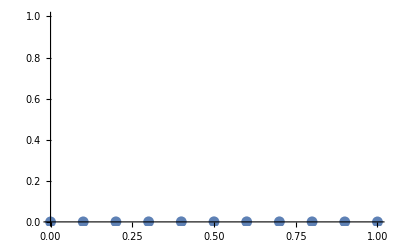
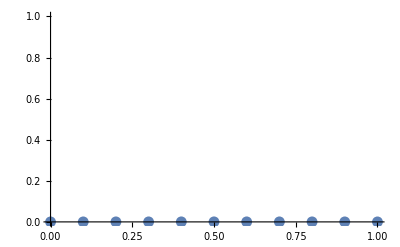
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[Tlist[n],PlotRange->{0,1}],{n,1,20}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
ρ[x_,y_]=x y
```

x y

```mathematica
a=1.;b=2.;
```

```mathematica
Mx=10;My=15;
```

```mathematica
Δx=a/Mx; Δy=b/My;
```

```mathematica
ϕ[0,k_]=0;
ϕ[Mx,k_]=0;
ϕ[j_,0]=0;
ϕ[j_,My]=0;
```

```mathematica
eqns=Table[(ϕ[j+1,k]-2ϕ[j,k]+ϕ[j-1,k])/Δx^2+(ϕ[j,k+1]-2ϕ[j,k]+ϕ[j,k-1])/Δy^2==ρ[j Δx, k Δy],{j,1,Mx-1},{k,1,My-1}]//Flatten
```

{56.25 (-2 ϕ[1,1]+ϕ[1,2])+100. (-2 ϕ[1,1]+ϕ[2,1])==0.0133333,56.25 (ϕ[1,1]-2 ϕ[1,2]+ϕ[1,3])+100. (-2 ϕ[1,2]+ϕ[2,2])==0.0266667,56.25 (ϕ[1,2]-2 ϕ[1,3]+ϕ[1,4])+100. (-2 ϕ[1,3]+ϕ[2,3])==0.04,56.25 (ϕ[1,3]-2 ϕ[1,4]+ϕ[1,5])+100. (-2 ϕ[1,4]+ϕ[2,4])==0.0533333,56.25 (ϕ[1,4]-2 ϕ[1,5]+ϕ[1,6])+100. (-2 ϕ[1,5]+ϕ[2,5])==0.0666667,56.25 (ϕ[1,5]-2 ϕ[1,6]+ϕ[1,7])+100. (-2 ϕ[1,6]+ϕ[2,6])==0.08,56.25 (ϕ[1,6]-2 ϕ[1,7]+ϕ[1,8])+100. (-2 ϕ[1,7]+ϕ[2,7])==0.0933333,56.25 (ϕ[1,7]-2 ϕ[1,8]+ϕ[1,9])+100. (-2 ϕ[1,8]+ϕ[2,8])==0.106667,56.25 (ϕ[1,8]-2 ϕ[1,9]+ϕ[1,10])+100. (-2 ϕ[1,9]+ϕ[2,9])==0.12,56.25 (ϕ[1,9]-2 ϕ[1,10]+ϕ[1,11])+100. (-2 ϕ[1,10]+ϕ[2,10])==0.133333,56.25 (ϕ[1,10]-2 ϕ[1,11]+ϕ[1,12])+100. (-2 ϕ[1,11]+ϕ[2,11])==0.146667,56.25 (ϕ[1,11]-2 ϕ[1,12]+ϕ[1,13])+100. (-2 ϕ[1,12]+ϕ[2,12])==0.16,56.25 (ϕ[1,12]-2 ϕ[1,13]+ϕ[1,14])+100. (-2 ϕ[1,13]+ϕ[2,13])==0.173333,56.25 (ϕ[1,13]-2 ϕ[1,14])+100. (-2 ϕ[1,14]+ϕ[2,14])==0.186667,56.25 (-2 ϕ[2,1]+ϕ[2,2])+100. (ϕ[1,1]-2 ϕ[2,1]+ϕ[3,1])==0.0266667,56.25 (ϕ[2,1]-2 ϕ[2,2]+ϕ[2,3])+100. (ϕ[1,2]-2 ϕ[2,2]+ϕ[3,2])==0.0533333,56.25 (ϕ[2,2]-2 ϕ[2,3]+ϕ[2,4])+100. (ϕ[1,3]-2 ϕ[2,3]+ϕ[3,3])==0.08,56.25 (ϕ[2,3]-2 ϕ[2,4]+ϕ[2,5])+100. (ϕ[1,4]-2 ϕ[2,4]+ϕ[3,4])==0.106667,56.25 (ϕ[2,4]-2 ϕ[2,5]+ϕ[2,6])+100. (ϕ[1,5]-2 ϕ[2,5]+ϕ[3,5])==0.133333,56.25 (ϕ[2,5]-2 ϕ[2,6]+ϕ[2,7])+100. (ϕ[1,6]-2 ϕ[2,6]+ϕ[3,6])==0.16,56.25 (ϕ[2,6]-2 ϕ[2,7]+ϕ[2,8])+100. (ϕ[1,7]-2 ϕ[2,7]+ϕ[3,7])==0.186667,56.25 (ϕ[2,7]-2 ϕ[2,8]+ϕ[2,9])+100. (ϕ[1,8]-2 ϕ[2,8]+ϕ[3,8])==0.213333,56.25 (ϕ[2,8]-2 ϕ[2,9]+ϕ[2,10])+100. (ϕ[1,9]-2 ϕ[2,9]+ϕ[3,9])==0.24,56.25 (ϕ[2,9]-2 ϕ[2,10]+ϕ[2,11])+100. (ϕ[1,10]-2 ϕ[2,10]+ϕ[3,10])==0.266667,56.25 (ϕ[2,10]-2 ϕ[2,11]+ϕ[2,12])+100. (ϕ[1,11]-2 ϕ[2,11]+ϕ[3,11])==0.293333,56.25 (ϕ[2,11]-2 ϕ[2,12]+ϕ[2,13])+100. (ϕ[1,12]-2 ϕ[2,12]+ϕ[3,12])==0.32,56.25 (ϕ[2,12]-2 ϕ[2,13]+ϕ[2,14])+100. (ϕ[1,13]-2 ϕ[2,13]+ϕ[3,13])==0.346667,56.25 (ϕ[2,13]-2 ϕ[2,14])+100. (ϕ[1,14]-2 ϕ[2,14]+ϕ[3,14])==0.373333,56.25 (-2 ϕ[3,1]+ϕ[3,2])+100. (ϕ[2,1]-2 ϕ[3,1]+ϕ[4,1])==0.04,56.25 (ϕ[3,1]-2 ϕ[3,2]+ϕ[3,3])+100. (ϕ[2,2]-2 ϕ[3,2]+ϕ[4,2])==0.08,56.25 (ϕ[3,2]-2 ϕ[3,3]+ϕ[3,4])+100. (ϕ[2,3]-2 ϕ[3,3]+ϕ[4,3])==0.12,56.25 (ϕ[3,3]-2 ϕ[3,4]+ϕ[3,5])+100. (ϕ[2,4]-2 ϕ[3,4]+ϕ[4,4])==0.16,56.25 (ϕ[3,4]-2 ϕ[3,5]+ϕ[3,6])+100. (ϕ[2,5]-2 ϕ[3,5]+ϕ[4,5])==0.2,56.25 (ϕ[3,5]-2 ϕ[3,6]+ϕ[3,7])+100. (ϕ[2,6]-2 ϕ[3,6]+ϕ[4,6])==0.24,56.25 (ϕ[3,6]-2 ϕ[3,7]+ϕ[3,8])+100. (ϕ[2,7]-2 ϕ[3,7]+ϕ[4,7])==0.28,56.25 (ϕ[3,7]-2 ϕ[3,8]+ϕ[3,9])+100. (ϕ[2,8]-2 ϕ[3,8]+ϕ[4,8])==0.32,56.25 (ϕ[3,8]-2 ϕ[3,9]+ϕ[3,10])+100. (ϕ[2,9]-2 ϕ[3,9]+ϕ[4,9])==0.36,56.25 (ϕ[3,9]-2 ϕ[3,10]+ϕ[3,11])+100. (ϕ[2,10]-2 ϕ[3,10]+ϕ[4,10])==0.4,56.25 (ϕ[3,10]-2 ϕ[3,11]+ϕ[3,12])+100. (ϕ[2,11]-2 ϕ[3,11]+ϕ[4,11])==0.44,56.25 (ϕ[3,11]-2 ϕ[3,12]+ϕ[3,13])+100. (ϕ[2,12]-2 ϕ[3,12]+ϕ[4,12])==0.48,56.25 (ϕ[3,12]-2 ϕ[3,13]+ϕ[3,14])+100. (ϕ[2,13]-2 ϕ[3,13]+ϕ[4,13])==0.52,56.25 (ϕ[3,13]-2 ϕ[3,14])+100. (ϕ[2,14]-2 ϕ[3,14]+ϕ[4,14])==0.56,56.25 (-2 ϕ[4,1]+ϕ[4,2])+100. (ϕ[3,1]-2 ϕ[4,1]+ϕ[5,1])==0.0533333,56.25 (ϕ[4,1]-2 ϕ[4,2]+ϕ[4,3])+100. (ϕ[3,2]-2 ϕ[4,2]+ϕ[5,2])==0.106667,56.25 (ϕ[4,2]-2 ϕ[4,3]+ϕ[4,4])+100. (ϕ[3,3]-2 ϕ[4,3]+ϕ[5,3])==0.16,56.25 (ϕ[4,3]-2 ϕ[4,4]+ϕ[4,5])+100. (ϕ[3,4]-2 ϕ[4,4]+ϕ[5,4])==0.213333,56.25 (ϕ[4,4]-2 ϕ[4,5]+ϕ[4,6])+100. (ϕ[3,5]-2 ϕ[4,5]+ϕ[5,5])==0.266667,56.25 (ϕ[4,5]-2 ϕ[4,6]+ϕ[4,7])+100. (ϕ[3,6]-2 ϕ[4,6]+ϕ[5,6])==0.32,56.25 (ϕ[4,6]-2 ϕ[4,7]+ϕ[4,8])+100. (ϕ[3,7]-2 ϕ[4,7]+ϕ[5,7])==0.373333,56.25 (ϕ[4,7]-2 ϕ[4,8]+ϕ[4,9])+100. (ϕ[3,8]-2 ϕ[4,8]+ϕ[5,8])==0.426667,56.25 (ϕ[4,8]-2 ϕ[4,9]+ϕ[4,10])+100. (ϕ[3,9]-2 ϕ[4,9]+ϕ[5,9])==0.48,56.25 (ϕ[4,9]-2 ϕ[4,10]+ϕ[4,11])+100. (ϕ[3,10]-2 ϕ[4,10]+ϕ[5,10])==0.533333,56.25 (ϕ[4,10]-2 ϕ[4,11]+ϕ[4,12])+100. (ϕ[3,11]-2 ϕ[4,11]+ϕ[5,11])==0.586667,56.25 (ϕ[4,11]-2 ϕ[4,12]+ϕ[4,13])+100. (ϕ[3,12]-2 ϕ[4,12]+ϕ[5,12])==0.64,56.25 (ϕ[4,12]-2 ϕ[4,13]+ϕ[4,14])+100. (ϕ[3,13]-2 ϕ[4,13]+ϕ[5,13])==0.693333,56.25 (ϕ[4,13]-2 ϕ[4,14])+100. (ϕ[3,14]-2 ϕ[4,14]+ϕ[5,14])==0.746667,56.25 (-2 ϕ[5,1]+ϕ[5,2])+100. (ϕ[4,1]-2 ϕ[5,1]+ϕ[6,1])==0.0666667,56.25 (ϕ[5,1]-2 ϕ[5,2]+ϕ[5,3])+100. (ϕ[4,2]-2 ϕ[5,2]+ϕ[6,2])==0.133333,56.25 (ϕ[5,2]-2 ϕ[5,3]+ϕ[5,4])+100. (ϕ[4,3]-2 ϕ[5,3]+ϕ[6,3])==0.2,56.25 (ϕ[5,3]-2 ϕ[5,4]+ϕ[5,5])+100. (ϕ[4,4]-2 ϕ[5,4]+ϕ[6,4])==0.266667,56.25 (ϕ[5,4]-2 ϕ[5,5]+ϕ[5,6])+100. (ϕ[4,5]-2 ϕ[5,5]+ϕ[6,5])==0.333333,56.25 (ϕ[5,5]-2 ϕ[5,6]+ϕ[5,7])+100. (ϕ[4,6]-2 ϕ[5,6]+ϕ[6,6])==0.4,56.25 (ϕ[5,6]-2 ϕ[5,7]+ϕ[5,8])+100. (ϕ[4,7]-2 ϕ[5,7]+ϕ[6,7])==0.466667,56.25 (ϕ[5,7]-2 ϕ[5,8]+ϕ[5,9])+100. (ϕ[4,8]-2 ϕ[5,8]+ϕ[6,8])==0.533333,56.25 (ϕ[5,8]-2 ϕ[5,9]+ϕ[5,10])+100. (ϕ[4,9]-2 ϕ[5,9]+ϕ[6,9])==0.6,56.25 (ϕ[5,9]-2 ϕ[5,10]+ϕ[5,11])+100. (ϕ[4,10]-2 ϕ[5,10]+ϕ[6,10])==0.666667,56.25 (ϕ[5,10]-2 ϕ[5,11]+ϕ[5,12])+100. (ϕ[4,11]-2 ϕ[5,11]+ϕ[6,11])==0.733333,56.25 (ϕ[5,11]-2 ϕ[5,12]+ϕ[5,13])+100. (ϕ[4,12]-2 ϕ[5,12]+ϕ[6,12])==0.8,56.25 (ϕ[5,12]-2 ϕ[5,13]+ϕ[5,14])+100. (ϕ[4,13]-2 ϕ[5,13]+ϕ[6,13])==0.866667,56.25 (ϕ[5,13]-2 ϕ[5,14])+100. (ϕ[4,14]-2 ϕ[5,14]+ϕ[6,14])==0.933333,56.25 (-2 ϕ[6,1]+ϕ[6,2])+100. (ϕ[5,1]-2 ϕ[6,1]+ϕ[7,1])==0.08,56.25 (ϕ[6,1]-2 ϕ[6,2]+ϕ[6,3])+100. (ϕ[5,2]-2 ϕ[6,2]+ϕ[7,2])==0.16,56.25 (ϕ[6,2]-2 ϕ[6,3]+ϕ[6,4])+100. (ϕ[5,3]-2 ϕ[6,3]+ϕ[7,3])==0.24,56.25 (ϕ[6,3]-2 ϕ[6,4]+ϕ[6,5])+100. (ϕ[5,4]-2 ϕ[6,4]+ϕ[7,4])==0.32,56.25 (ϕ[6,4]-2 ϕ[6,5]+ϕ[6,6])+100. (ϕ[5,5]-2 ϕ[6,5]+ϕ[7,5])==0.4,56.25 (ϕ[6,5]-2 ϕ[6,6]+ϕ[6,7])+100. (ϕ[5,6]-2 ϕ[6,6]+ϕ[7,6])==0.48,56.25 (ϕ[6,6]-2 ϕ[6,7]+ϕ[6,8])+100. (ϕ[5,7]-2 ϕ[6,7]+ϕ[7,7])==0.56,56.25 (ϕ[6,7]-2 ϕ[6,8]+ϕ[6,9])+100. (ϕ[5,8]-2 ϕ[6,8]+ϕ[7,8])==0.64,56.25 (ϕ[6,8]-2 ϕ[6,9]+ϕ[6,10])+100. (ϕ[5,9]-2 ϕ[6,9]+ϕ[7,9])==0.72,56.25 (ϕ[6,9]-2 ϕ[6,10]+ϕ[6,11])+100. (ϕ[5,10]-2 ϕ[6,10]+ϕ[7,10])==0.8,56.25 (ϕ[6,10]-2 ϕ[6,11]+ϕ[6,12])+100. (ϕ[5,11]-2 ϕ[6,11]+ϕ[7,11])==0.88,56.25 (ϕ[6,11]-2 ϕ[6,12]+ϕ[6,13])+100. (ϕ[5,12]-2 ϕ[6,12]+ϕ[7,12])==0.96,56.25 (ϕ[6,12]-2 ϕ[6,13]+ϕ[6,14])+100. (ϕ[5,13]-2 ϕ[6,13]+ϕ[7,13])==1.04,56.25 (ϕ[6,13]-2 ϕ[6,14])+100. (ϕ[5,14]-2 ϕ[6,14]+ϕ[7,14])==1.12,56.25 (-2 ϕ[7,1]+ϕ[7,2])+100. (ϕ[6,1]-2 ϕ[7,1]+ϕ[8,1])==0.0933333,56.25 (ϕ[7,1]-2 ϕ[7,2]+ϕ[7,3])+100. (ϕ[6,2]-2 ϕ[7,2]+ϕ[8,2])==0.186667,56.25 (ϕ[7,2]-2 ϕ[7,3]+ϕ[7,4])+100. (ϕ[6,3]-2 ϕ[7,3]+ϕ[8,3])==0.28,56.25 (ϕ[7,3]-2 ϕ[7,4]+ϕ[7,5])+100. (ϕ[6,4]-2 ϕ[7,4]+ϕ[8,4])==0.373333,56.25 (ϕ[7,4]-2 ϕ[7,5]+ϕ[7,6])+100. (ϕ[6,5]-2 ϕ[7,5]+ϕ[8,5])==0.466667,56.25 (ϕ[7,5]-2 ϕ[7,6]+ϕ[7,7])+100. (ϕ[6,6]-2 ϕ[7,6]+ϕ[8,6])==0.56,56.25 (ϕ[7,6]-2 ϕ[7,7]+ϕ[7,8])+100. (ϕ[6,7]-2 ϕ[7,7]+ϕ[8,7])==0.653333,56.25 (ϕ[7,7]-2 ϕ[7,8]+ϕ[7,9])+100. (ϕ[6,8]-2 ϕ[7,8]+ϕ[8,8])==0.746667,56.25 (ϕ[7,8]-2 ϕ[7,9]+ϕ[7,10])+100. (ϕ[6,9]-2 ϕ[7,9]+ϕ[8,9])==0.84,56.25 (ϕ[7,9]-2 ϕ[7,10]+ϕ[7,11])+100. (ϕ[6,10]-2 ϕ[7,10]+ϕ[8,10])==0.933333,56.25 (ϕ[7,10]-2 ϕ[7,11]+ϕ[7,12])+100. (ϕ[6,11]-2 ϕ[7,11]+ϕ[8,11])==1.02667,56.25 (ϕ[7,11]-2 ϕ[7,12]+ϕ[7,13])+100. (ϕ[6,12]-2 ϕ[7,12]+ϕ[8,12])==1.12,56.25 (ϕ[7,12]-2 ϕ[7,13]+ϕ[7,14])+100. (ϕ[6,13]-2 ϕ[7,13]+ϕ[8,13])==1.21333,56.25 (ϕ[7,13]-2 ϕ[7,14])+100. (ϕ[6,14]-2 ϕ[7,14]+ϕ[8,14])==1.30667,56.25 (-2 ϕ[8,1]+ϕ[8,2])+100. (ϕ[7,1]-2 ϕ[8,1]+ϕ[9,1])==0.106667,56.25 (ϕ[8,1]-2 ϕ[8,2]+ϕ[8,3])+100. (ϕ[7,2]-2 ϕ[8,2]+ϕ[9,2])==0.213333,56.25 (ϕ[8,2]-2 ϕ[8,3]+ϕ[8,4])+100. (ϕ[7,3]-2 ϕ[8,3]+ϕ[9,3])==0.32,56.25 (ϕ[8,3]-2 ϕ[8,4]+ϕ[8,5])+100. (ϕ[7,4]-2 ϕ[8,4]+ϕ[9,4])==0.426667,56.25 (ϕ[8,4]-2 ϕ[8,5]+ϕ[8,6])+100. (ϕ[7,5]-2 ϕ[8,5]+ϕ[9,5])==0.533333,56.25 (ϕ[8,5]-2 ϕ[8,6]+ϕ[8,7])+100. (ϕ[7,6]-2 ϕ[8,6]+ϕ[9,6])==0.64,56.25 (ϕ[8,6]-2 ϕ[8,7]+ϕ[8,8])+100. (ϕ[7,7]-2 ϕ[8,7]+ϕ[9,7])==0.746667,56.25 (ϕ[8,7]-2 ϕ[8,8]+ϕ[8,9])+100. (ϕ[7,8]-2 ϕ[8,8]+ϕ[9,8])==0.853333,56.25 (ϕ[8,8]-2 ϕ[8,9]+ϕ[8,10])+100. (ϕ[7,9]-2 ϕ[8,9]+ϕ[9,9])==0.96,56.25 (ϕ[8,9]-2 ϕ[8,10]+ϕ[8,11])+100. (ϕ[7,10]-2 ϕ[8,10]+ϕ[9,10])==1.06667,56.25 (ϕ[8,10]-2 ϕ[8,11]+ϕ[8,12])+100. (ϕ[7,11]-2 ϕ[8,11]+ϕ[9,11])==1.17333,56.25 (ϕ[8,11]-2 ϕ[8,12]+ϕ[8,13])+100. (ϕ[7,12]-2 ϕ[8,12]+ϕ[9,12])==1.28,56.25 (ϕ[8,12]-2 ϕ[8,13]+ϕ[8,14])+100. (ϕ[7,13]-2 ϕ[8,13]+ϕ[9,13])==1.38667,56.25 (ϕ[8,13]-2 ϕ[8,14])+100. (ϕ[7,14]-2 ϕ[8,14]+ϕ[9,14])==1.49333,100. (ϕ[8,1]-2 ϕ[9,1])+56.25 (-2 ϕ[9,1]+ϕ[9,2])==0.12,100. (ϕ[8,2]-2 ϕ[9,2])+56.25 (ϕ[9,1]-2 ϕ[9,2]+ϕ[9,3])==0.24,100. (ϕ[8,3]-2 ϕ[9,3])+56.25 (ϕ[9,2]-2 ϕ[9,3]+ϕ[9,4])==0.36,100. (ϕ[8,4]-2 ϕ[9,4])+56.25 (ϕ[9,3]-2 ϕ[9,4]+ϕ[9,5])==0.48,100. (ϕ[8,5]-2 ϕ[9,5])+56.25 (ϕ[9,4]-2 ϕ[9,5]+ϕ[9,6])==0.6,100. (ϕ[8,6]-2 ϕ[9,6])+56.25 (ϕ[9,5]-2 ϕ[9,6]+ϕ[9,7])==0.72,100. (ϕ[8,7]-2 ϕ[9,7])+56.25 (ϕ[9,6]-2 ϕ[9,7]+ϕ[9,8])==0.84,100. (ϕ[8,8]-2 ϕ[9,8])+56.25 (ϕ[9,7]-2 ϕ[9,8]+ϕ[9,9])==0.96,100. (ϕ[8,9]-2 ϕ[9,9])+56.25 (ϕ[9,8]-2 ϕ[9,9]+ϕ[9,10])==1.08,100. (ϕ[8,10]-2 ϕ[9,10])+56.25 (ϕ[9,9]-2 ϕ[9,10]+ϕ[9,11])==1.2,100. (ϕ[8,11]-2 ϕ[9,11])+56.25 (ϕ[9,10]-2 ϕ[9,11]+ϕ[9,12])==1.32,100. (ϕ[8,12]-2 ϕ[9,12])+56.25 (ϕ[9,11]-2 ϕ[9,12]+ϕ[9,13])==1.44,100. (ϕ[8,13]-2 ϕ[9,13])+56.25 (ϕ[9,12]-2 ϕ[9,13]+ϕ[9,14])==1.56,100. (ϕ[8,14]-2 ϕ[9,14])+56.25 (ϕ[9,13]-2 ϕ[9,14])==1.68}

```mathematica
Length[eqns]
```

126

```mathematica
vars=Table[ϕ[j,k],{j,1,Mx-1},{k,1,My-1}]//Flatten
```

{ϕ[1,1],ϕ[1,2],ϕ[1,3],ϕ[1,4],ϕ[1,5],ϕ[1,6],ϕ[1,7],ϕ[1,8],ϕ[1,9],ϕ[1,10],ϕ[1,11],ϕ[1,12],ϕ[1,13],ϕ[1,14],ϕ[2,1],ϕ[2,2],ϕ[2,3],ϕ[2,4],ϕ[2,5],ϕ[2,6],ϕ[2,7],ϕ[2,8],ϕ[2,9],ϕ[2,10],ϕ[2,11],ϕ[2,12],ϕ[2,13],ϕ[2,14],ϕ[3,1],ϕ[3,2],ϕ[3,3],ϕ[3,4],ϕ[3,5],ϕ[3,6],ϕ[3,7],ϕ[3,8],ϕ[3,9],ϕ[3,10],ϕ[3,11],ϕ[3,12],ϕ[3,13],ϕ[3,14],ϕ[4,1],ϕ[4,2],ϕ[4,3],ϕ[4,4],ϕ[4,5],ϕ[4,6],ϕ[4,7],ϕ[4,8],ϕ[4,9],ϕ[4,10],ϕ[4,11],ϕ[4,12],ϕ[4,13],ϕ[4,14],ϕ[5,1],ϕ[5,2],ϕ[5,3],ϕ[5,4],ϕ[5,5],ϕ[5,6],ϕ[5,7],ϕ[5,8],ϕ[5,9],ϕ[5,10],ϕ[5,11],ϕ[5,12],ϕ[5,13],ϕ[5,14],ϕ[6,1],ϕ[6,2],ϕ[6,3],ϕ[6,4],ϕ[6,5],ϕ[6,6],ϕ[6,7],ϕ[6,8],ϕ[6,9],ϕ[6,10],ϕ[6,11],ϕ[6,12],ϕ[6,13],ϕ[6,14],ϕ[7,1],ϕ[7,2],ϕ[7,3],ϕ[7,4],ϕ[7,5],ϕ[7,6],ϕ[7,7],ϕ[7,8],ϕ[7,9],ϕ[7,10],ϕ[7,11],ϕ[7,12],ϕ[7,13],ϕ[7,14],ϕ[8,1],ϕ[8,2],ϕ[8,3],ϕ[8,4],ϕ[8,5],ϕ[8,6],ϕ[8,7],ϕ[8,8],ϕ[8,9],ϕ[8,10],ϕ[8,11],ϕ[8,12],ϕ[8,13],ϕ[8,14],ϕ[9,1],ϕ[9,2],ϕ[9,3],ϕ[9,4],ϕ[9,5],ϕ[9,6],ϕ[9,7],ϕ[9,8],ϕ[9,9],ϕ[9,10],ϕ[9,11],ϕ[9,12],ϕ[9,13],ϕ[9,14]}

```mathematica
Solve[eqns,vars]
```

{{ϕ[1,1]→-0.00213203,ϕ[1,2]→-0.00425229,ϕ[1,3]→-0.00634697,ϕ[1,4]→-0.00839793,ϕ[1,5]→-0.0103796,ϕ[1,6]→-0.0122548,ϕ[1,7]→-0.0139689,ϕ[1,8]→-0.0154413,ϕ[1,9]→-0.016554,ϕ[1,10]→-0.0171361,ϕ[1,11]→-0.0169449,ϕ[1,12]→-0.0156443,ϕ[1,13]→-0.0127853,ϕ[1,14]→-0.00779712,ϕ[2,1]→-0.00413736,ϕ[2,2]→-0.00825229,ϕ[2,3]→-0.0123185,ϕ[2,4]→-0.0163015,ϕ[2,5]→-0.0201524,ϕ[2,6]→-0.0238003,ϕ[2,7]→-0.0271405,ϕ[2,8]→-0.0300183,ϕ[2,9]→-0.0322063,ϕ[2,10]→-0.0333738,ϕ[2,11]→-0.0330473,ϕ[2,12]→-0.0305652,ϕ[2,13]→-0.0250348,ϕ[2,14]→-0.0153076,ϕ[3,1]→-0.00588863,ϕ[3,2]→-0.0117464,ϕ[3,3]→-0.017537,ϕ[3,4]→-0.0232127,ϕ[3,5]→-0.0287061,ϕ[3,6]→-0.0339189,ϕ[3,7]→-0.0387055,ϕ[3,8]→-0.0428499,ϕ[3,9]→-0.0460328,ϕ[3,10]→-0.0477853,ϕ[3,11]→-0.0474288,ϕ[3,12]→-0.0440008,ϕ[3,13]→-0.0361784,ϕ[3,14]→-0.0222238,ϕ[4,1]→-0.00725728,ϕ[4,2]→-0.0144782,ϕ[4,3]→-0.02162,ϕ[4,4]→-0.0286264,ϕ[4,5]→-0.0354177,ϕ[4,6]→-0.0418772,ϕ[4,7]→-0.0478316,ϕ[4,8]→-0.0530224,ϕ[4,9]→-0.0570638,ϕ[4,10]→-0.0593831,ϕ[4,11]→-0.0591379,ϕ[4,12]→-0.0551083,ϕ[4,13]→-0.0455714,ϕ[4,14]→-0.0281913,ϕ[5,1]→-0.00811306,ϕ[5,2]→-0.0161878,ϕ[5,3]→-0.0241792,ϕ[5,4]→-0.0320278,ϕ[5,5]→-0.0396492,ϕ[5,6]→-0.0469195,ϕ[5,7]→-0.053654,ϕ[5,8]→-0.0595749,ϕ[5,9]→-0.0642636,ϕ[5,10]→-0.0670901,ϕ[5,11]→-0.0671091,ϕ[5,12]→-0.0629136,ϕ[5,13]→-0.0524429,ϕ[5,14]→-0.0327735,ϕ[6,1]→-0.00832374,ϕ[6,2]→-0.016611,ϕ[6,3]→-0.0248187,ϕ[6,4]→-0.0328903,ϕ[6,5]→-0.0407448,ϕ[6,6]→-0.0482633,ϕ[6,7]→-0.0552674,ϕ[6,8]→-0.061487,ϕ[6,9]→-0.0665108,ϕ[6,10]→-0.0697096,ϕ[6,11]→-0.0701176,ϕ[6,12]→-0.0662487,ϕ[6,13]→-0.0558221,ϕ[6,14]→-0.0353933,ϕ[7,1]→-0.00775497,ϕ[7,2]→-0.0154788,ϕ[7,3]→-0.0231349,ϕ[7,4]→-0.0306748,ϕ[7,5]→-0.0380294,ϕ[7,6]→-0.0450965,ϕ[7,7]→-0.0517222,ϕ[7,8]→-0.0576719,ϕ[7,9]→-0.0625845,ϕ[7,10]→-0.0658989,ϕ[7,11]→-0.066732,ϕ[7,12]→-0.0636726,ϕ[7,13]→-0.0544275,ϕ[7,14]→-0.0352306,ϕ[8,1]→-0.00627037,ϕ[8,2]→-0.0125181,ϕ[8,3]→-0.0187165,ϕ[8,4]→-0.0248303,ϕ[8,5]→-0.030809,ϕ[8,6]→-0.0365779,ϕ[8,7]→-0.0420238,ϕ[8,8]→-0.0469734,ϕ[8,9]→-0.0511572,ϕ[8,10]→-0.0541506,ϕ[8,11]→-0.0552692,ϕ[8,12]→-0.0533758,ϕ[8,13]→-0.0464974,ϕ[8,14]→-0.0310201,ϕ[9,1]→-0.00373183,ϕ[9,2]→-0.00745175,ϕ[9,3]→-0.0111457,ϕ[9,4]→-0.0147952,ϕ[9,5]→-0.0183734,ϕ[9,6]→-0.021841,ϕ[9,7]→-0.025138,ϕ[9,8]→-0.0281722,ϕ[9,9]→-0.0307996,ϕ[9,10]→-0.0327902,ϕ[9,11]→-0.0337674,ϕ[9,12]→-0.0330832,ϕ[9,13]→-0.0295376,ϕ[9,14]→-0.0206192}}

```mathematica
ϕlist=Table[{j Δx, k Δy, ϕ[j,k]},{j,0,Mx},{k,0,My}]/.%34[[1]]
```

{{{0.,0.,0},{0.,0.133333,0},{0.,0.266667,0},{0.,0.4,0},{0.,0.533333,0},{0.,0.666667,0},{0.,0.8,0},{0.,0.933333,0},{0.,1.06667,0},{0.,1.2,0},{0.,1.33333,0},{0.,1.46667,0},{0.,1.6,0},{0.,1.73333,0},{0.,1.86667,0},{0.,2.,0}},{{0.1,0.,0},{0.1,0.133333,-0.00213203},{0.1,0.266667,-0.00425229},{0.1,0.4,-0.00634697},{0.1,0.533333,-0.00839793},{0.1,0.666667,-0.0103796},{0.1,0.8,-0.0122548},{0.1,0.933333,-0.0139689},{0.1,1.06667,-0.0154413},{0.1,1.2,-0.016554},{0.1,1.33333,-0.0171361},{0.1,1.46667,-0.0169449},{0.1,1.6,-0.0156443},{0.1,1.73333,-0.0127853},{0.1,1.86667,-0.00779712},{0.1,2.,0}},{{0.2,0.,0},{0.2,0.133333,-0.00413736},{0.2,0.266667,-0.00825229},{0.2,0.4,-0.0123185},{0.2,0.533333,-0.0163015},{0.2,0.666667,-0.0201524},{0.2,0.8,-0.0238003},{0.2,0.933333,-0.0271405},{0.2,1.06667,-0.0300183},{0.2,1.2,-0.0322063},{0.2,1.33333,-0.0333738},{0.2,1.46667,-0.0330473},{0.2,1.6,-0.0305652},{0.2,1.73333,-0.0250348},{0.2,1.86667,-0.0153076},{0.2,2.,0}},{{0.3,0.,0},{0.3,0.133333,-0.00588863},{0.3,0.266667,-0.0117464},{0.3,0.4,-0.017537},{0.3,0.533333,-0.0232127},{0.3,0.666667,-0.0287061},{0.3,0.8,-0.0339189},{0.3,0.933333,-0.0387055},{0.3,1.06667,-0.0428499},{0.3,1.2,-0.0460328},{0.3,1.33333,-0.0477853},{0.3,1.46667,-0.0474288},{0.3,1.6,-0.0440008},{0.3,1.73333,-0.0361784},{0.3,1.86667,-0.0222238},{0.3,2.,0}},{{0.4,0.,0},{0.4,0.133333,-0.00725728},{0.4,0.266667,-0.0144782},{0.4,0.4,-0.02162},{0.4,0.533333,-0.0286264},{0.4,0.666667,-0.0354177},{0.4,0.8,-0.0418772},{0.4,0.933333,-0.0478316},{0.4,1.06667,-0.0530224},{0.4,1.2,-0.0570638},{0.4,1.33333,-0.0593831},{0.4,1.46667,-0.0591379},{0.4,1.6,-0.0551083},{0.4,1.73333,-0.0455714},{0.4,1.86667,-0.0281913},{0.4,2.,0}},{{0.5,0.,0},{0.5,0.133333,-0.00811306},{0.5,0.266667,-0.0161878},{0.5,0.4,-0.0241792},{0.5,0.533333,-0.0320278},{0.5,0.666667,-0.0396492},{0.5,0.8,-0.0469195},{0.5,0.933333,-0.053654},{0.5,1.06667,-0.0595749},{0.5,1.2,-0.0642636},{0.5,1.33333,-0.0670901},{0.5,1.46667,-0.0671091},{0.5,1.6,-0.0629136},{0.5,1.73333,-0.0524429},{0.5,1.86667,-0.0327735},{0.5,2.,0}},{{0.6,0.,0},{0.6,0.133333,-0.00832374},{0.6,0.266667,-0.016611},{0.6,0.4,-0.0248187},{0.6,0.533333,-0.0328903},{0.6,0.666667,-0.0407448},{0.6,0.8,-0.0482633},{0.6,0.933333,-0.0552674},{0.6,1.06667,-0.061487},{0.6,1.2,-0.0665108},{0.6,1.33333,-0.0697096},{0.6,1.46667,-0.0701176},{0.6,1.6,-0.0662487},{0.6,1.73333,-0.0558221},{0.6,1.86667,-0.0353933},{0.6,2.,0}},{{0.7,0.,0},{0.7,0.133333,-0.00775497},{0.7,0.266667,-0.0154788},{0.7,0.4,-0.0231349},{0.7,0.533333,-0.0306748},{0.7,0.666667,-0.0380294},{0.7,0.8,-0.0450965},{0.7,0.933333,-0.0517222},{0.7,1.06667,-0.0576719},{0.7,1.2,-0.0625845},{0.7,1.33333,-0.0658989},{0.7,1.46667,-0.066732},{0.7,1.6,-0.0636726},{0.7,1.73333,-0.0544275},{0.7,1.86667,-0.0352306},{0.7,2.,0}},{{0.8,0.,0},{0.8,0.133333,-0.00627037},{0.8,0.266667,-0.0125181},{0.8,0.4,-0.0187165},{0.8,0.533333,-0.0248303},{0.8,0.666667,-0.030809},{0.8,0.8,-0.0365779},{0.8,0.933333,-0.0420238},{0.8,1.06667,-0.0469734},{0.8,1.2,-0.0511572},{0.8,1.33333,-0.0541506},{0.8,1.46667,-0.0552692},{0.8,1.6,-0.0533758},{0.8,1.73333,-0.0464974},{0.8,1.86667,-0.0310201},{0.8,2.,0}},{{0.9,0.,0},{0.9,0.133333,-0.00373183},{0.9,0.266667,-0.00745175},{0.9,0.4,-0.0111457},{0.9,0.533333,-0.0147952},{0.9,0.666667,-0.0183734},{0.9,0.8,-0.021841},{0.9,0.933333,-0.025138},{0.9,1.06667,-0.0281722},{0.9,1.2,-0.0307996},{0.9,1.33333,-0.0327902},{0.9,1.46667,-0.0337674},{0.9,1.6,-0.0330832},{0.9,1.73333,-0.0295376},{0.9,1.86667,-0.0206192},{0.9,2.,0}},{{1.,0.,0},{1.,0.133333,0},{1.,0.266667,0},{1.,0.4,0},{1.,0.533333,0},{1.,0.666667,0},{1.,0.8,0},{1.,0.933333,0},{1.,1.06667,0},{1.,1.2,0},{1.,1.33333,0},{1.,1.46667,0},{1.,1.6,0},{1.,1.73333,0},{1.,1.86667,0},{1.,2.,0}}}

```mathematica
Flatten[ϕlist,1]
```

{{0.,0.,0},{0.,0.133333,0},{0.,0.266667,0},{0.,0.4,0},{0.,0.533333,0},{0.,0.666667,0},{0.,0.8,0},{0.,0.933333,0},{0.,1.06667,0},{0.,1.2,0},{0.,1.33333,0},{0.,1.46667,0},{0.,1.6,0},{0.,1.73333,0},{0.,1.86667,0},{0.,2.,0},{0.1,0.,0},{0.1,0.133333,-0.00213203},{0.1,0.266667,-0.00425229},{0.1,0.4,-0.00634697},{0.1,0.533333,-0.00839793},{0.1,0.666667,-0.0103796},{0.1,0.8,-0.0122548},{0.1,0.933333,-0.0139689},{0.1,1.06667,-0.0154413},{0.1,1.2,-0.016554},{0.1,1.33333,-0.0171361},{0.1,1.46667,-0.0169449},{0.1,1.6,-0.0156443},{0.1,1.73333,-0.0127853},{0.1,1.86667,-0.00779712},{0.1,2.,0},{0.2,0.,0},{0.2,0.133333,-0.00413736},{0.2,0.266667,-0.00825229},{0.2,0.4,-0.0123185},{0.2,0.533333,-0.0163015},{0.2,0.666667,-0.0201524},{0.2,0.8,-0.0238003},{0.2,0.933333,-0.0271405},{0.2,1.06667,-0.0300183},{0.2,1.2,-0.0322063},{0.2,1.33333,-0.0333738},{0.2,1.46667,-0.0330473},{0.2,1.6,-0.0305652},{0.2,1.73333,-0.0250348},{0.2,1.86667,-0.0153076},{0.2,2.,0},{0.3,0.,0},{0.3,0.133333,-0.00588863},{0.3,0.266667,-0.0117464},{0.3,0.4,-0.017537},{0.3,0.533333,-0.0232127},{0.3,0.666667,-0.0287061},{0.3,0.8,-0.0339189},{0.3,0.933333,-0.0387055},{0.3,1.06667,-0.0428499},{0.3,1.2,-0.0460328},{0.3,1.33333,-0.0477853},{0.3,1.46667,-0.0474288},{0.3,1.6,-0.0440008},{0.3,1.73333,-0.0361784},{0.3,1.86667,-0.0222238},{0.3,2.,0},{0.4,0.,0},{0.4,0.133333,-0.00725728},{0.4,0.266667,-0.0144782},{0.4,0.4,-0.02162},{0.4,0.533333,-0.0286264},{0.4,0.666667,-0.0354177},{0.4,0.8,-0.0418772},{0.4,0.933333,-0.0478316},{0.4,1.06667,-0.0530224},{0.4,1.2,-0.0570638},{0.4,1.33333,-0.0593831},{0.4,1.46667,-0.0591379},{0.4,1.6,-0.0551083},{0.4,1.73333,-0.0455714},{0.4,1.86667,-0.0281913},{0.4,2.,0},{0.5,0.,0},{0.5,0.133333,-0.00811306},{0.5,0.266667,-0.0161878},{0.5,0.4,-0.0241792},{0.5,0.533333,-0.0320278},{0.5,0.666667,-0.0396492},{0.5,0.8,-0.0469195},{0.5,0.933333,-0.053654},{0.5,1.06667,-0.0595749},{0.5,1.2,-0.0642636},{0.5,1.33333,-0.0670901},{0.5,1.46667,-0.0671091},{0.5,1.6,-0.0629136},{0.5,1.73333,-0.0524429},{0.5,1.86667,-0.0327735},{0.5,2.,0},{0.6,0.,0},{0.6,0.133333,-0.00832374},{0.6,0.266667,-0.016611},{0.6,0.4,-0.0248187},{0.6,0.533333,-0.0328903},{0.6,0.666667,-0.0407448},{0.6,0.8,-0.0482633},{0.6,0.933333,-0.0552674},{0.6,1.06667,-0.061487},{0.6,1.2,-0.0665108},{0.6,1.33333,-0.0697096},{0.6,1.46667,-0.0701176},{0.6,1.6,-0.0662487},{0.6,1.73333,-0.0558221},{0.6,1.86667,-0.0353933},{0.6,2.,0},{0.7,0.,0},{0.7,0.133333,-0.00775497},{0.7,0.266667,-0.0154788},{0.7,0.4,-0.0231349},{0.7,0.533333,-0.0306748},{0.7,0.666667,-0.0380294},{0.7,0.8,-0.0450965},{0.7,0.933333,-0.0517222},{0.7,1.06667,-0.0576719},{0.7,1.2,-0.0625845},{0.7,1.33333,-0.0658989},{0.7,1.46667,-0.066732},{0.7,1.6,-0.0636726},{0.7,1.73333,-0.0544275},{0.7,1.86667,-0.0352306},{0.7,2.,0},{0.8,0.,0},{0.8,0.133333,-0.00627037},{0.8,0.266667,-0.0125181},{0.8,0.4,-0.0187165},{0.8,0.533333,-0.0248303},{0.8,0.666667,-0.030809},{0.8,0.8,-0.0365779},{0.8,0.933333,-0.0420238},{0.8,1.06667,-0.0469734},{0.8,1.2,-0.0511572},{0.8,1.33333,-0.0541506},{0.8,1.46667,-0.0552692},{0.8,1.6,-0.0533758},{0.8,1.73333,-0.0464974},{0.8,1.86667,-0.0310201},{0.8,2.,0},{0.9,0.,0},{0.9,0.133333,-0.00373183},{0.9,0.266667,-0.00745175},{0.9,0.4,-0.0111457},{0.9,0.533333,-0.0147952},{0.9,0.666667,-0.0183734},{0.9,0.8,-0.021841},{0.9,0.933333,-0.025138},{0.9,1.06667,-0.0281722},{0.9,1.2,-0.0307996},{0.9,1.33333,-0.0327902},{0.9,1.46667,-0.0337674},{0.9,1.6,-0.0330832},{0.9,1.73333,-0.0295376},{0.9,1.86667,-0.0206192},{0.9,2.,0},{1.,0.,0},{1.,0.133333,0},{1.,0.266667,0},{1.,0.4,0},{1.,0.533333,0},{1.,0.666667,0},{1.,0.8,0},{1.,0.933333,0},{1.,1.06667,0},{1.,1.2,0},{1.,1.33333,0},{1.,1.46667,0},{1.,1.6,0},{1.,1.73333,0},{1.,1.86667,0},{1.,2.,0}}

```mathematica
ϕfun=Interpolation[Flatten[ϕlist,1]]
```

InterpolatingFunction[{{0., 1.}, {0., 2.}}, <>]

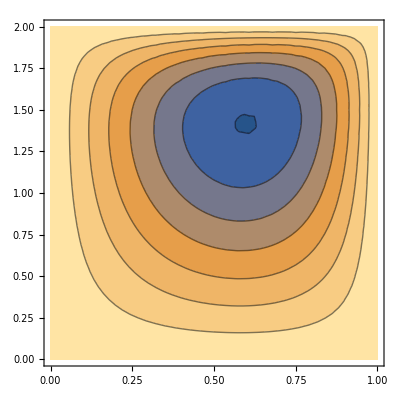

```mathematica
ContourPlot[ϕfun[x,y],{x,0,a},{y,0,b}]
```